```mathematica
files = FileNames["*.tab"];
datas = Drop[Import[#], 1]&/@files;
ch1s=Transpose[{#[[All,1]],#[[All,2]]}]&/@datas;
ch2s=Transpose[{#[[All,1]],#[[All,3]]}]&/@datas;
data = Transpose[{ch1s, ch2s}];
filterdata = data[[ ;; 13]];
foehndata = data[[14 ;; ]];
```

```mathematica
fitrange={{0,0.0011},{0,0.0045},{0,0.0033},{0,0.0047},{0,0.003},{0,0.0038},{0,0.0048},{0,0.0064},{0,0.008},{0,0.01},{0,0.01},{0,0.02},{0,0.042}};
fitdata =Table[Select[filterdata[[i, 1]], #[[1]]≥ fitrange[[i,1]] && #[[1]]≤fitrange[[i,2]]&],{i,{1,2,3,4,5,6,7,8,9,10,11,12,13}}];
```

```mathematica
ListPlot[filterdata[[#,1]]&/@Range[13],ImageSize->900,Frame->True]
```

## nlm1

```mathematica
nlm= NonlinearModelFit[fitdata[[3]],{ a/(1+Exp[(-x+μ)/(σ*10^-3)])+b-Piecewise[{{0,x<μ},{ c Exp[-d x],x≥μ}}],a<10,b<0,b>-0.1,c>0,c<5,d>0,d<1000,σ>0,σ<0.1,μ<0.005,μ>0.004}, {{a,2},{b,-0.07},{μ,0.0043},{σ,0.03},{c,2},{d,500}}, x]
nlm["ParameterTable"]
```

## nlm2

```mathematica
startval={{
{a,1},{b,0},{μ,1},{σ,10},{c,1},{d,10}},
{{a,1},{b,0},{μ,1},{σ,10},{c,0.2},{d,7}},
{{a,1.22},{b,-0.05},{μ,1.7},{σ,10},{c,0.15},{d,2}},
{{a,1.22},{b,-0.05},{μ,2.7},{σ,10},{c,0.2},{d,1}},
{{a,1.2},{b,-0.05},{μ,1.3},{σ,10},{c,0.15},{d,1}},
{{a,1.2},{b,-0.05},{μ,1.3},{σ,10},{c,0.15},{d,1}},
{{a,1.5},{b,-0.05},{μ,3.4},{σ,10},{c,0.15},{d,10}},
{{a,1.5},{b,-0.05},{μ,4.3},{σ,10},{c,0.15},{d,10}},
{{a,1.5},{b,-0.05},{μ,5.4},{σ,10},{c,0.15},{d,10}},
{{a,1.5},{b,-0.05},{μ,6.6},{σ,10},{c,0.15},{d,10}},
{{a,1.5},{b,-0.05},{μ,5.1},{σ,10},{c,0.15},{d,10}},
{{a,1.5},{b,-0.05},{μ,11},{σ,10},{c,0.15},{d,10}},
{{a,1.3},{b,-0.05},{μ,30},{σ,1},{c,0.15},{d,10}}
};
Conμup={3,3,3,3,3,3,4,5,6,7,7,12,40};
Conddown={1,1,1,0.1,1,1,0.1,1,1,0.1,0.1,0.1,0.02};
fitvals={};
nlms={};
Do[
nlm= NonlinearModelFit[fitdata[[n]],
{a/(1+Exp[(-x+μ*10^-3)/(σ*10^-6)])+b+Piecewise[{{0,x<μ*10^-3},{ c(1- Exp[-d*10^3 (x-μ*10^-3)]),x≥μ*10^-3}}],
0.1<a,a<2,-1<b,b<1,0.5<μ,μ<Conμup[[n]],0.1<σ,σ<100,0.001<c,c<10,Conddown[[n]]<d,d<100}, startval[[n]], x];
Quiet[fitvals=Append[fitvals,nlm["ParameterTableEntries"]]];
nlms=Append[nlms,nlm];
Print[n];
Quiet[Print[nlm["ParameterTable"]]],
{n,1,13}]
```

1

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.37217 | 0.0116408 | 31.9711 | 2.93926×10^-116
b | -0.0641534 | 0.000307587 | -208.57 | 4.38198022342×10^-438
μ | 0.698894 | 0.000189219 | 3693.57 | 4.08881295636×10^-980
σ | 6.67488 | 0.142255 | 46.9219 | 2.59035×10^-172
c | 0.957742 | 0.0115547 | 82.8875 | 1.3347×10^-268
d | 32.2022 | 0.209995 | 153.347 | 9.0614000504×10^-381

2

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.26605 | 0.00141804 | 892.819 | 2.00157110375×10^-2379
b | -0.0640796 | 0.000324495 | -197.475 | 6.66297515348×10^-1220
μ | 1.84252 | 0.000104956 | 17555.1 | 1.231817574×10^-4700
σ | 13.1647 | 0.0899851 | 146.298 | 6.62405167667×10^-1000
c | 0.139015 | 0.00119606 | 116.228 | 9.23914500824×10^-838
d | 1.39927 | 0.0311633 | 44.9014 | 8.70606×10^-296

3

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.2292 | 0.00242387 | 507.124 | 3.99864559055×10^-852
b | -0.0640705 | 0.000402024 | -159.37 | 4.17344325452×10^-526
μ | 1.68864 | 0.000139694 | 12088.2 | 7.33963044242×10^-1754
σ | 13.6718 | 0.116144 | 117.715 | 7.24078968455×10^-443
c | 0.148154 | 0.0020247 | 73.1733 | 1.87143103838×10^-317
d | 2.32942 | 0.0783473 | 29.732 | 1.29694×10^-123

4

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.23826 | 0.00169793 | 729.277 | 1.28861039932×10^-1290
b | -0.0637374 | 0.000267606 | -238.176 | 3.58812567832×10^-839
μ | 2.74401 | 0.000119545 | 22953.9 | 7.41376825159×10^-2691
σ | 14.8845 | 0.100837 | 147.61 | 4.23227171872×10^-650
c | 0.152197 | 0.00140167 | 108.583 | 2.27198383248×10^-532
d | 1.66101 | 0.0444627 | 37.3574 | 1.23804×10^-187

5

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.21016 | 0.00272399 | 444.259 | 6.56682409560957×10^-419
b | -0.0634134 | 0.000577096 | -109.884 | 2.23385×10^-241
μ | 1.30666 | 0.000195006 | 6700.59 | 1.82640181891258×10^-766
σ | 16.5476 | 0.162749 | 101.675 | 1.09815×10^-231
c | 0.164209 | 0.00220157 | 74.587 | 1.70246×10^-193
d | 1.63866 | 0.0734103 | 22.3219 | 2.51902×10^-65

6

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.21878 | 0.00324367 | 375.742 | 2.7951795711×10^-485
b | -0.06333 | 0.000461565 | -137.207 | 1.34122157193×10^-322
μ | 2.40055 | 0.000220301 | 10896.7 | 1.82117362021×10^-1033
σ | 16.9587 | 0.180839 | 93.7775 | 2.07605×10^-262
c | 0.158439 | 0.00286807 | 55.2426 | 3.02176×10^-182
d | 1.68908 | 0.111055 | 15.2095 | 4.95686×10^-41

7

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.23003 | 0.00252274 | 487.575 | 1.78959264548×10^-643
b | -0.0647716 | 0.000302883 | -213.85 | 2.58556416993×10^-474
μ | 3.41986 | 0.000229037 | 14931.5 | 3.79227220687×10^-1349
σ | 26.8982 | 0.182194 | 147.635 | 4.94316860859×10^-399
c | 0.174288 | 0.00789593 | 22.0732 | 7.88485×10^-75
d | 0.920424 | 0.0960365 | 9.58411 | 5.23691×10^-20

8

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.19653 | 0.00250938 | 476.821 | 1.743233446×10^-813
b | -0.0641571 | 0.000337251 | -190.235 | 4.33046774867×10^-562
μ | 4.35379 | 0.000223189 | 19507.2 | 1.27936111984×10^-1836
σ | 18.7944 | 0.187321 | 100.333 | 1.10497231521×10^-391
c | 0.183527 | 0.00219846 | 83.4799 | 1.48243685049×10^-344
d | 1.24541 | 0.052065 | 23.9202 | 1.20243×10^-90

9

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.20186 | 0.00213356 | 563.31 | 1.18049132161×10^-1036
b | -0.0632036 | 0.000297609 | -212.372 | 1.96481872682×10^-702
μ | 5.40047 | 0.00022602 | 23893.8 | 4.07500866124×10^-2330
σ | 20.7937 | 0.191081 | 108.821 | 9.05163519649×10^-480
c | 0.190832 | 0.00188478 | 101.249 | 1.53057457901×10^-456
d | 1.00006 | 0.0339575 | 29.4505 | 1.79089×10^-129

10

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.20161 | 0.00183922 | 653.323 | 1.84002548715×10^-1312
b | -0.0638948 | 0.000262443 | -243.461 | 5.3607981701×10^-889
μ | 6.62877 | 0.000221444 | 29934.3 | 1.07389058979×10^-2964
σ | 21.6913 | 0.189014 | 114.76 | 4.03872676257×10^-576
c | 0.198681 | 0.00156052 | 127.317 | 3.97718246466×10^-618
d | 0.8842 | 0.0218747 | 40.4211 | 3.87396×10^-212

11

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.19399 | 0.00347217 | 343.875 | 1.853379377114×10^-491
b | -0.063061 | 0.000652223 | -96.6862 | 4.69409×10^-277
μ | 5.12684 | 0.000557252 | 9200.22 | 5.377978535909×10^-1055
σ | 28.4853 | 0.474702 | 60.0068 | 1.37018×10^-200
c | 0.213713 | 0.00290982 | 73.4456 | 2.13129×10^-232
d | 0.695183 | 0.0265326 | 26.2011 | 2.03866×10^-88

12

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.18657 | 0.00287856 | 412.209 | 3.34184532452×10^-929
b | -0.0631721 | 0.000407957 | -154.85 | 5.55685940677×10^-596
μ | 11.1135 | 0.000577922 | 19230.1 | 3.82369085783×10^-2255
σ | 35.6017 | 0.493115 | 72.1976 | 2.22623156744×10^-351
c | 0.219425 | 0.00266581 | 82.3109 | 2.68474085235×10^-391
d | 0.664392 | 0.0143369 | 46.3415 | 3.97283×10^-228

13

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.21936 | 0.00432978 | 281.621 | 7.56083575984×10^-830
b | -0.0625911 | 0.000400241 | -156.384 | 1.03612421979×10^-620
μ | 29.7478 | 0.00140071 | 21237.7 | 1.28710359099×10^-2395
σ | 76.37 | 1.16414 | 65.6021 | 1.01030002104×10^-331
c | 0.191176 | 0.00401284 | 47.641 | 2.49386×10^-240
d | 0.476045 | 0.0169825 | 28.0315 | 2.20629×10^-122

{-0.521419,1.19111,1.14512,1.1498,1.10936,1.12367,1.12051,1.07716,1.07423,1.06682,1.04334,1.03032,1.09077}

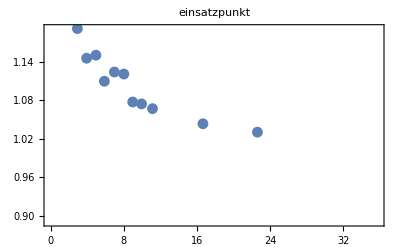

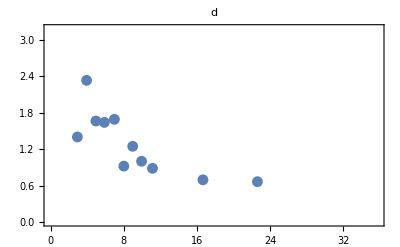

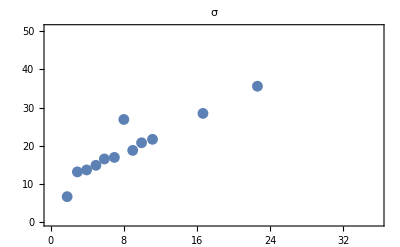

```mathematica
einsatzpunkt=fitvals[[All,1,1]]-fitvals[[All,2,1]]-fitvals[[All,5,1]]
ListPlot[Transpose[{T,einsatzpunkt}],PlotLabel->"einsatzpunkt",Frame->True]
ListPlot[Transpose[{T,fitvals[[All,6,1]]}],PlotLabel->"d",Frame->True]
ListPlot[Transpose[{T,fitvals[[All,4,1]]}],PlotLabel->"σ",Frame->True]
```

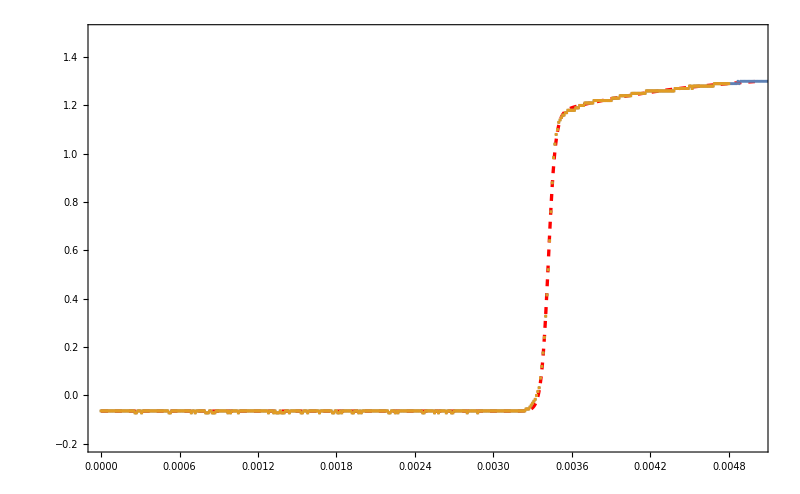

```mathematica
nr=7;
nr2=7;
Show[Plot[Normal[nlms[[nr2]]],{x,0,0.005},ImageSize->800,Frame->True,PlotRange->{-0.2,1.5},ImageSize->500,Frame->True, PlotStyle->{Red, Dashed,Thickness->0.003}],ListPlot[{filterdata[[nr,1]],fitdata[[nr]]},PlotMarkers->{Automatic,3}]]
```

```mathematica
Manipulate[Show[Plot[{Normal[nlm],a/(1+Exp[(-x+μ*10^-3)/(σ*10^-6)])+b+Piecewise[{{0,x<μ*10^-3},{ c(1- Exp[-d*10^3 (x-μ*10^-3)]),x≥μ*10^-3}}]},{x,0,0.01},ImageSize->600,Frame->True,PlotRange->{-0.2,1.5},Frame->True, PlotStyle->{Red, Dashed,3}],ListPlot[{filterdata[[n,1]],fitdata[[n]]},PlotMarkers->{Automatic,1}]],{{a,1.23},0,5},{{b,0.05},-2,2},{{μ,1.8},0.7,3},{{σ,10},1,20},{{c,0.11},0,2},{{d,9300},0,10000}]
```

```mathematica
ListPlot[filterdata[[7,1]],ImageSize->700,Frame->True]
```

```mathematica
einsatz={{{0.0007778,1.186}},{{0.001905,1.179}},{{0.001759,1.175}},{{0.002808,1.169}},{{0.001421,1.16}},{{0.002485,1.158}},{{0.003456,1.143}},{{0.004395,1.13}},{{0.005459,1.119}},{{0.006711,1.112}},{{0.005196,1.115}},{{0.01114,1.097}},{{0.03011,1.161}}};
fallend={{{0.002593,0.6409}},{{0.004839,0.6786}},{{0.005703,0.6157}},{{0.007769,0.7189}},{{0.007306,0.7321}},{{0.009466,0.7529}},{{0.01147,0.7529}},{{0.01338,0.672}},{{0.01541,0.6945}},{{0.01786,0.6394}},{{0.02186,0.6795}},{{0.03376,0.6269}},{{0.08176,0.647}}};
```

{1.186,1.179,1.175,1.169,1.16,1.158,1.143,1.13,1.119,1.112,1.115,1.097,1.161}

{1.8152,2.934,3.944,4.961,5.885,6.981,8.014,8.985,9.951,11.149,16.664,22.62,51.65}

{{1.8152,1.186},{2.934,1.179},{3.944,1.175},{4.961,1.169},{5.885,1.16},{6.981,1.158},{8.014,1.143},{8.985,1.13},{9.951,1.119},{11.149,1.112},{16.664,1.115},{22.62,1.097},{51.65,1.161}}

{{1.8152,1.186},{2.934,1.179},{3.944,1.175},{4.961,1.169},{5.885,1.16},{6.981,1.158},{8.014,1.143},{8.985,1.13},{9.951,1.119},{11.149,1.112}}

FittedModel[1.09335+0.12 ⅇ^(-0.116905 x)]

FittedModel::constr: The property values {"ParameterTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a | 8.55393 | 8.7754 | 0.974762 | 0.362152
min | 1.09335 | 0.0606636 | 18.0231 | 4.00083×10^-7
amp | 0.12 | 0.0453137 | 2.64821 | 0.0330276

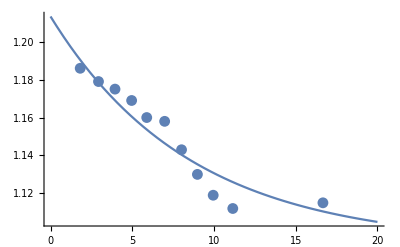

```mathematica
einsatz2=einsatz[[All,1,2]]
T=(fallend[[All,1,1]]-einsatz[[All,1,1]])*10^3
plotdata=Transpose[{T,einsatz2}]
fitdata=Drop[plotdata,-3]
nlm=NonlinearModelFit[fitdata,{min+amp Exp[-x/a],amp>0,amp<0.12},{a,min,amp},x]
nlm["ParameterTable"]
Show[Plot[Normal[nlm],{x,0,20}],ListPlot[plotdata,PlotRange->{1,1.3}]]
```